```mathematica
(*SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/pressure/D/v95/rmax95/eb1"];fnumber=5500;*)
(*SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/pressure/D/v95/rmax95/eb01"];fnumber=8900;*)
(*SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/pressure/D/v95/rmax95/eb001"];fnumber=8900;*)
(*SetDirectory["/Users/JMB/Documents/code/bem3d_ves_tube/pressure/D/v95/rmax95/eb0001"];fnumber=7900;*)

(* filenames *)
vesfile = StringJoin["vesicle",IntegerString[fnumber,10,6],".dat"];
(*vesfile=StringJoin["pro_v95_N10242_E20480.dat"];*)

(* import data *)
data=Import[vesfile];

(* get XYZ data *)
NNodes = ToExpression[StringDrop[data[[3,2]],2]];
NFaces = ToExpression[StringDrop[data[[3,3]],2]];
points=data[[4;;(3+NNodes),1;;3]];
polys=data[[(4+NNodes);;,1;;3]];
xavg = Mean[points[[All,1]]] ;yavg = Mean[points[[All,2]]];zavg = Mean[points[[All,3]]];
points[[All,1]]=points[[All,1]]-xavg; 
facecenters=Table[(1/3)*Sum[points[[polys[[j]][[i]]]],{i,1,3}],{j,1,NFaces}];

(* get normal velocity, pressure, and tension *)
vn =data[[4;;(3+NNodes),4]];
fn =data[[4;;(3+NNodes),5]];
fnbend =data[[4;;(3+NNodes),6]];
fntens =data[[4;;(3+NNodes),7]];
tens =data[[4;;(3+NNodes),8]];

(* set image size *)
IMSize=900;

(* length *)
length=Max[points[[All,1]]]-Min[points[[All,1]]]

(* projected radius *)
rproj=Max[points[[All,2]],points[[All,3]]]-1

(* mean tension *)
meantens = Mean[tens[[All]]]
```

2.85471

0.949515

82.8576

-Graphics3D-

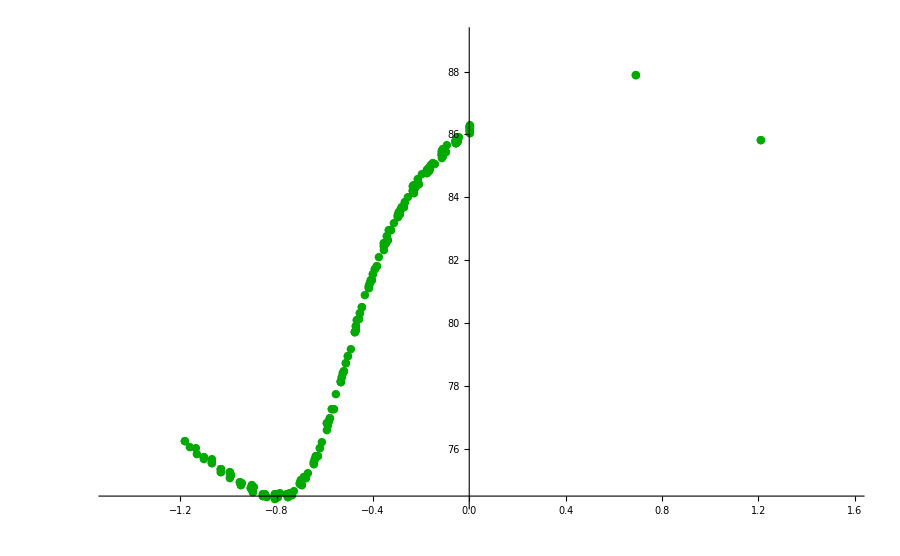

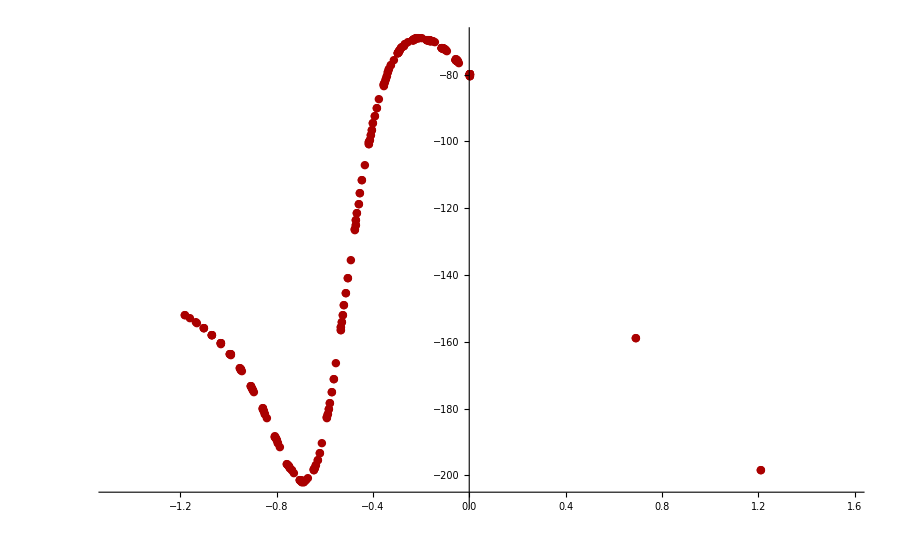

```mathematica
(* vesicle mesh *)
g1=Graphics3D[{Table[Polygon[{points[[polys[[i,1]]]],points[[polys[[i,2]]]],points[[polys[[i,3]]]]}],{i,1,2*NNodes-4}]}, PlotRange->Automatic, ImageSize->IMSize, Boxed-> False, ViewPoint-> Front];Show[g1]

(* plot tension data *)
g2=ListPlot[Table[{points[[i,1]],tens[[i]]},{i,1,NNodes}], PlotRange->{{Min[points[[All,1]]]-0.1, Max[points[[All,1]]]+0.1},{Min[tens]-1,Max[tens]}+1}, ImageSize->IMSize(*{{1280,1280},{720,720}}*),PlotStyle-> Darker[Green],PlotMarkers->{Automatic,Medium}(*,Epilog-> Inset[g1,{(Min[points[[All,1]]]+Max[points[[All,1]]])/2,Min[tensions]-5}]*)]; Show[g2]

(* plot pressure data *)
g3=ListPlot[Table[{points[[i,1]],-fn[[i]]},{i,1,NNodes}], PlotRange->{{Min[points[[All,1]]]-0.1, Max[points[[All,1]]]+0.1},{Min[-fn],Max[-fn]}}, ImageSize->IMSize(*{{1280,1280},{720,720}}*),PlotStyle-> Darker[Red],PlotMarkers->{Automatic,Medium}(*,Epilog-> Inset[g1,{(Min[points[[All,1]]]+Max[points[[All,1]]])/2,Min[tensions]-5}]*)]; Show[g3]
```

```mathematica
(* export data to file *)
shapeOutput={points[[All,1]],points[[All,2]],points[[All,3]]};
pressOutput={facecenters[[All,1]],Flatten[-fn]};
tensOutput={points[[All,1]],Flatten[tens]};
Export[StringJoin["shape",".dat"],shapeOutput]
Export[StringJoin["press",".dat"],pressOutput]
Export[StringJoin["tens",".dat"],tensOutput]
```

shape.dat

press.dat

tens.dat

```mathematica
Mean[tensions]
Mean[pressures]
```

Mean[$Failed⟦2;;5763⟧]

Mean[$Failed⟦2;;11521⟧]